```mathematica
dateMouseSessionListV1={{"071720","Mouse21019","Session2"},{"082520","Mouse21020","Session2"},{"072520","Mouse21036","Session1"},{"072820","Mouse21036","Session1"},{"080820","Mouse21062","Session1"},{"091420","Mouse21068","Session2"},{"091720","Mouse21068","Session1"},{"091720","Mouse23336","Session1"},{"092120","Mouse23336","Session1"},{"111220","Mouse23385","Session1"},{"120420","Mouse23385","Session1"},{"120920","Mouse23312","Session2"},{"121120","Mouse23312","Session3"},{"011121","Mouse23332","Session1"},{"011321","Mouse23332","Session2"},{"011721","Mouse23332","Session2"},{"011321","Mouse23305","Session2"},{"011721","Mouse23305","Session2"},{"031121","Mouse23321","Session1"},{"031821","Mouse23321","Session3"}};
```

```mathematica
dateMouseSessionListV2m={{"121619","Mouse20031","Session2"},{"121919","Mouse20033","Session1"},{"122219","Mouse20033","Session1"},{"092120","Mouse21011","Session1"},{"120720","Mouse23383","Session2"},{"022821","Mouse23310","Session1"},{"030321","Mouse23338","Session1"},{"031721","Mouse23338","Session1"}};
```

```mathematica
(********************************************************)
```

```mathematica
suppIndexValsV1=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/suppressionIndices_V1.txt","List"];
```

```mathematica
suppIndexValsV2m=ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/suppressionIndices_V2m.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
v1Charts=Show[BoxWhiskerChart[suppIndexValsV1,{{"Whiskers", Directive[Darker@Blue,Thick]}, {"Fences", Directive[Darker@Blue,Thick]},{"MedianMarker", Directive[Darker@Blue,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False],DistributionChart[suppIndexValsV1,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[BoxWhiskerChart[suppIndexValsV2m,{{"Whiskers", Directive[Darker@Purple,Thick]}, {"Fences", Directive[Darker@Purple,Thick]},{"MedianMarker", Directive[Darker@Purple,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False],DistributionChart[suppIndexValsV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[suppIndexValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,1.8}},ChartStyle->Transparent,Frame->False],DistributionChart[suppIndexValsV2m,PlotRange->{All,{0,1.8}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,1.8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

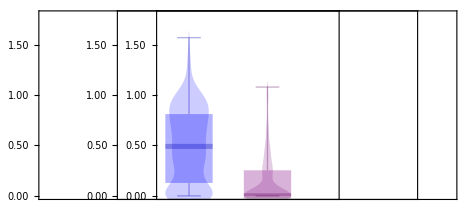

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```